```mathematica
f[x_,y_]=Sin[√(x^2+y^2)]
```

Sin[√(x^2+y^2)]

```mathematica
gradf[x_,y_]={D[f[x,y],x],D[f[x,y],y]}
```

{(x Cos[√(x^2+y^2)])/(√(x^2+y^2)),(y Cos[√(x^2+y^2)])/(√(x^2+y^2))}

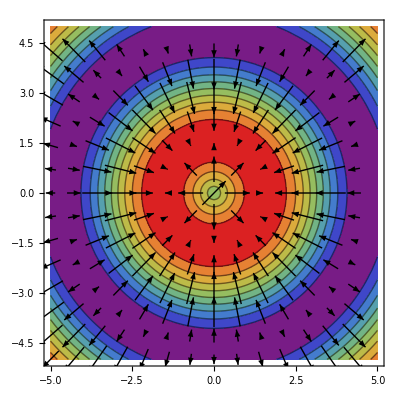

```mathematica
Show[
ContourPlot[f[x,y],{x,-5,5},{y,-5,5},ColorFunction->"Rainbow"],
VectorPlot[gradf[x,y],{x,-5,5},{y,-5,5},VectorStyle->Black]
]
```

```mathematica
field[x_,y_,z_]={z^2,x^2,y^2}
```

{z^2,x^2,y^2}

```mathematica
VectorPlot3D[field[x,y,z],{x,-3,3},{y,-3,3},{z,-3,3}, VectorPoints->2]
```

VectorPlot3D::strmpts: None is not a valid StreamPoints specification.